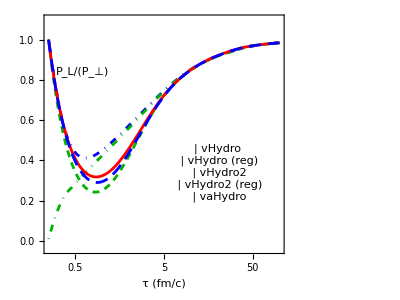

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH=Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]];

stylesVH2=Directive[RGBColor[0,0.7,0],AbsoluteThickness[2],AbsoluteDashing[{5,4}]];

stylesVHreg=Directive[RGBColor[0,0,1],AbsoluteThickness[2],DotDashed];

stylesVH2reg=Directive[RGBColor[0,0.7,0],AbsoluteThickness[2],DotDashed];

stylesblack=Directive[RGBColor[0,0,0],AbsoluteThickness[1.2]];

stylesVAH=Directive[RGBColor[1,0,0],AbsoluteThickness[2]];


min = {0.0085,0};
maj={0.0145,0};

timeticks = {{0.3,"",min},{0.4,"",min},{0.5,"0.5",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,1,maj},{2,"",min},{3,"",min},{4,"",min},{5,5,maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,10,maj},{20,"",min},{30,"",min},{40,"",min},{50,50,maj},{60,"",min},{70,"",min},{80,"",min},{90,"",min},{100,100,maj}};

notimeticks = {{0.3,"",min},{0.4,"",min},{0.5,"",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",maj},{60,"",min},{70,"",min},{80,"",min},{90,"",min},{100,"",maj}};


loglogticks = {{0.0001,"",min},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,0.1,maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,1,maj}};

nologlogticks = {{0.0001,"",min},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,"",maj}};



(*//////////////////////////////////////////////////////////////*)

plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];
plptDataRawVHreg=Import[wd<>"/plptplot_vh_reg.dat"];

plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];
plptDataVHreg= Take[plptDataRawVHreg,{2,Length[plptDataRawVHreg]}];

plptVH = Interpolation[plptDataVH[[All,{1,2}]]];
plptVHreg = Interpolation[plptDataVHreg[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)

plptDataRawVH2=Import[wd<>"/plptplot_vh_limit.dat"];
plptDataRawVH2reg=Import[wd<>"/plptplot_vh2_reg.dat"];

plptDataVH2= Take[plptDataRawVH2,{2,Length[plptDataRawVH2]}];
plptDataVH2reg= Take[plptDataRawVH2reg,{2,Length[plptDataRawVH2reg]}];

plptVH2 = Interpolation[plptDataVH2[[All,{1,2}]]];
plptVH2reg = Interpolation[plptDataVH2reg[[All,{1,2}]]];





PiNSDataRawVH=Import[wd<>"/bulkNSplot_vh.dat"];
PiNSDataVH= Take[PiNSDataRawVH,{2,Length[PiNSDataRawVH]}];
bulkNSVH = Interpolation[PiNSDataVH[[All,{1,2}]]];

piNSDataRawVH=Import[wd<>"/piNSplot_vh.dat"];
piNSDataVH= Take[piNSDataRawVH,{2,Length[piNSDataRawVH]}];
piNSVH = Interpolation[piNSDataVH[[All,{1,2}]]];



PiNSDataRawVH2=Import[wd<>"/bulkNSplot_vh_limit.dat"];
PiNSDataVH2= Take[PiNSDataRawVH2,{2,Length[PiNSDataRawVH2]}];
bulkNSVH2 = Interpolation[PiNSDataVH2[[All,{1,2}]]];

piNSDataRawVH2=Import[wd<>"/piNSplot_vh_limit.dat"];
piNSDataVH2= Take[piNSDataRawVH2,{2,Length[piNSDataRawVH2]}];
piNSVH2 = Interpolation[piNSDataVH2[[All,{1,2}]]];



PiNSDataRawVAH=Import[wd<>"/bulkNSplot_vah.dat"];
PiNSDataVAH= Take[PiNSDataRawVAH,{2,Length[PiNSDataRawVAH]}];
bulkNSVAH = Interpolation[PiNSDataVAH[[All,{1,2}]]];

piNSDataRawVAH=Import[wd<>"/piNSplot_vah.dat"];
piNSDataVAH= Take[piNSDataRawVAH,{2,Length[piNSDataRawVAH]}];
piNSVAH = Interpolation[piNSDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)


t0 =plptDataVAH[[1,1]];
tf = plptDataVAH[[Length[plptDataVAH],1]];


legend1=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->36,AspectRatio->0.2],Style["vHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVHreg,Line[{{0,0},{1,0}}]},ImageSize->36,AspectRatio->0.2],Style["vHydro (reg)",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2,Line[{{0,0},{1,0}}]},ImageSize->36
,AspectRatio->0.2],Style["vHydro2",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2reg,Line[{{0,0},{1,0}}]},ImageSize->36
,AspectRatio->0.2],Style["vHydro2 (reg)",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->36
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legend2=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vHydro",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->28
,AspectRatio->0.2],Style["vaHydro",FontSize->16,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


legendplpt=Panel[Style["P_L/(P_⊥)",FontSize->24,FontFamily->"Calibri"],Background->White,FrameMargins->0];



a=30;
b=20;


plptplot =LogLinearPlot[{plptVHreg[t],plptVH2reg[t],plptVH2[t],plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->{-0.04,1.1},PlotStyle->{stylesVHreg,stylesVH2reg,stylesVH2,stylesVAH,stylesVH},ImageSize->400,FrameLabel->Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendplpt,{-0.5,0.84}],Inset[legend1,{3.0,0.34}]}(*,ImagePadding->{{a,b},{Automatic,Automatic}}*)]


a1=Panel[GraphicsGrid[{{plptplot}},Spacings->{-5,-41}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Appearance->"Frameless",Background->White,ImageSize->{738,300},FrameMargins->0];

Export["plptplot.pdf",plptplot];
```

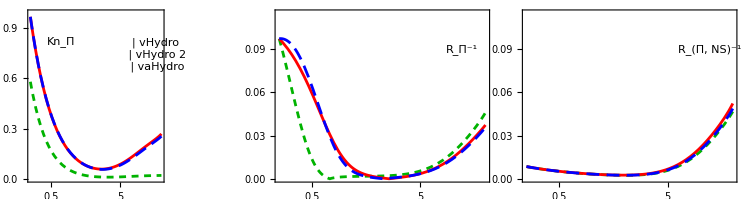
-Graphics-τ (fm/c)

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVH2=Import[wd<>"/RpiInvplot_vh_limit.dat"];
RbulkInverseDataRawVH2=Import[wd<>"/RbulkInvplot_vh_limit.dat"];

RpiInverseDataVH2= Take[RpiInverseDataRawVH2,{2,Length[RpiInverseDataRawVH2]}];
RbulkInverseDataVH2= Take[RbulkInverseDataRawVH2,{2,Length[RbulkInverseDataRawVH2]}];

RpiInverseVH2 = Interpolation[RpiInverseDataVH2[[All,{1,2}]]];
RbulkInverseVH2 = Interpolation[RbulkInverseDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVAH=Import[wd<>"/RpiInvplot_vah.dat"];
RbulkInverseDataRawVAH=Import[wd<>"/RbulkInvplot_vah.dat"];

RpiInverseDataVAH= Take[RpiInverseDataRawVAH,{2,Length[RpiInverseDataRawVAH]}];
RbulkInverseDataVAH= Take[RbulkInverseDataRawVAH,{2,Length[RbulkInverseDataRawVAH]}];

RpiInverseVAH = Interpolation[RpiInverseDataVAH[[All,{1,2}]]];
RbulkInverseVAH = Interpolation[RbulkInverseDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH=Import[wd<>"/taupiplot_vh.dat"];
taubulkDataRawVH=Import[wd<>"/taubulkplot_vh.dat"];

taupiDataVH= Take[taupiDataRawVH,{2,Length[taupiDataRawVH]}];
taubulkDataVH= Take[taubulkDataRawVH,{2,Length[taubulkDataRawVH]}];

taupiVH = Interpolation[taupiDataVH[[All,{1,2}]]];
taubulkVH = Interpolation[taubulkDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH2=Import[wd<>"/taupiplot_vh_limit.dat"];
taubulkDataRawVH2=Import[wd<>"/taubulkplot_vh_limit.dat"];

taupiDataVH2= Take[taupiDataRawVH2,{2,Length[taupiDataRawVH2]}];
taubulkDataVH2= Take[taubulkDataRawVH2,{2,Length[taubulkDataRawVH2]}];

taupiVH2 = Interpolation[taupiDataVH2[[All,{1,2}]]];
taubulkVH2 = Interpolation[taubulkDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVAH=Import[wd<>"/taupiplot_vah.dat"];
taubulkDataRawVAH=Import[wd<>"/taubulkplot_vah.dat"];

taupiDataVAH= Take[taupiDataRawVAH,{2,Length[taupiDataRawVAH]}];
taubulkDataVAH= Take[taubulkDataRawVAH,{2,Length[taubulkDataRawVAH]}];

taupiVAH = Interpolation[taupiDataVAH[[All,{1,2}]]];
taubulkVAH = Interpolation[taubulkDataVAH[[All,{1,2}]]];



RbulkInverseDataRawVAH2=Import[wd<>"/RbulkInvplot_vah_bulk_2.dat"];
RbulkInverseDataVAH2= Take[RbulkInverseDataRawVAH2,{2,Length[RbulkInverseDataRawVAH2]}];
RbulkInverseVAH2 = Interpolation[RbulkInverseDataVAH2[[All,{1,2}]]];


taubulkDataRawVAH2=Import[wd<>"/taubulkplot_vah_bulk_2.dat"];
taubulkDataVAH2= Take[taubulkDataRawVAH2,{2,Length[taubulkDataRawVAH2]}];
taubulkVAH2 = Interpolation[taubulkDataVAH2[[All,{1,2}]]];


legend1=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro 2",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


legendRbulk=Panel[Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRpi=Panel[Style["R_π^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRbulkNS=Panel[Style["R_(Π, NS)^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendRpiNS=Panel[Style["R_(π, NS)^-1",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendKnbulk=Panel[Style["Kn_Π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendKnpi=Panel[Style["Kn_π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];

a=30;
b = 20;

stylesVAH2=Directive[RGBColor[0.5,0,0.9],AbsoluteThickness[2],AbsoluteDashing[{8.,4.6}]];


Knbulk=LogLinearPlot[{taubulkVH2[t]/t,taubulkVAH[t]/t,taubulkVH[t]/t},{t,t0,tf-0.005},PlotRange->{0,0.99},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9.2,5.}]],stylesVAH2},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendKnbulk,{-0.35,0.82}],Inset[legend1,{2.8,0.74}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Rbulk=LogLinearPlot[{Abs[RbulkInverseVH2[t]],Abs[RbulkInverseVAH[t]],Abs[RbulkInverseVH[t]]},{t,t0,tf},PlotRange->{-0.00,0.115},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5.}]],stylesVAH2},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},RotateLabel->False(*FrameLabel->{"","","",Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"]}*),BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendRbulk,{2.5,0.09}]},ImagePadding->{{a,b},{Automatic,Automatic}}];


RbulkNS=LogLinearPlot[{Abs[bulkNSVH2[t]],Abs[bulkNSVAH[t]],Abs[bulkNSVH[t]]},{t,t0,tf},PlotRange->{-0.00,0.115},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9.2,5.3}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendRbulkNS,{2.5,0.09}]},ImagePadding->{{a,b},{Automatic,Automatic}}];


(*a3=Panel[GraphicsGrid[{{Rpi,Rbulk},{Knpi,Knbulk}},Spacings->{-49,-24.3}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{420,325},FrameMargins->0]
*)
a3=Panel[GraphicsGrid[{{Knbulk,Rbulk,RbulkNS}},Spacings->{-5,0}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{743,200},FrameMargins->0]

Export["bulkplot.pdf",a3];
```

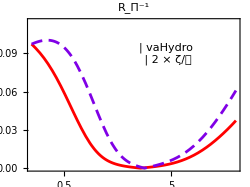

```mathematica
stylesVAH2=Directive[RGBColor[0.5,0,0.9],AbsoluteThickness[2],AbsoluteDashing[{8.1,4.6}]];

legend2=Panel[Grid[{
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH2,Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["2 × ζ/𝒮",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

Rbulk=LogLinearPlot[{Abs[RbulkInverseVAH[t]],Abs[RbulkInverseVAH2[t]]},{t,t0,tf},PlotRange->{-0.00,0.115},PlotStyle->{stylesVAH,stylesVAH2},FrameLabel->{Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14]},PlotLabel->legendRbulk,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{timeticks,notimeticks}},RotateLabel->False(*FrameLabel->{"","","",Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"]}*),BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend2,{1.5,0.09}]},ImagePadding->{{a,b},{Automatic,Automatic}}]

Export["bulkplot2.pdf",Rbulk];
```

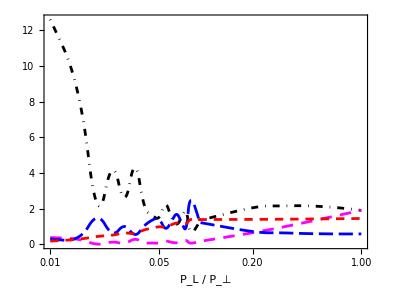

```mathematica
PLPT = {0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};


ax =Reverse[{1.905,
1.957,
2.008,
2.059,
2.105,
2.145,
2.17,
2.159,
2.053,
1.427,
1.191,
0.7255,
1.82,
1.54,
1.14,
1.56,
2.22,
1.52,
1.65,
2.29,
4.3,
2.63,
4.14,
2.3,
8.53,
12.6}];

az=Reverse[{1.905,
1.823,
1.728,
1.619,
1.492,
1.342,
1.164,
0.9437,
0.658,
0.225,
0.1589,
0.0756,
0.217,
0.157,
0.0943,
0.125,
0.185,
0.0875,
0.0805,
0.108,
0.285,
0.0734,
0.13,
0.0207,
0.289,
0.385}];

BoverBeq=Reverse[{1.454,
1.45,
1.445,
1.44,
1.434,
1.428,
1.421,
1.413,
1.404,
1.395,
1.394,
1.393,
1.18,
1.19,
1.2,
1.1,
0.973,
0.987,
0.91,
0.805,
0.618,
0.638,
0.52,
0.444,
0.291,
0.187}];

LambdaoverT=Reverse[{0.2948,
0.2941,
0.2941,
0.2949,
0.2972,
0.3015,
0.3096,
0.3253,
0.3629,
0.5847,
0.7189,
1.228,
0.501,
0.605,
0.841,
0.633,
0.456,
0.701,
0.675,
0.505,
0.279,
0.502,
0.333,
0.736,
0.195,
0.156}]/0.5;

Length[LambdaoverT];
Length[PLPT];

axplot=Table[{PLPT[[i]],ax[[i]]},{i,1,Length[PLPT]}];
azplot=Table[{PLPT[[i]],az[[i]]},{i,1,Length[PLPT]}];
LambdaoverTplot=Table[{PLPT[[i]],LambdaoverT[[i]]},{i,1,Length[PLPT]}];
BoverBeqplot=Table[{PLPT[[i]],BoverBeq[[i]]},{i,1,Length[PLPT]}];

stylesdB=Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{6,5}]];

stylesax=Directive[Black,AbsoluteThickness[2],DotDashed];stylesaz=Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8.25,6}]];
stylesLambda=Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10.2,4.1}]];


legendinit=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,0],AbsoluteThickness[2],DotDashed],Line[{{0,0},{1,0}}]},ImageSize->40,AspectRatio->0.2],Style["α_⊥",FontSize->18,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->40,AspectRatio->0.2],Style["α_L",FontSize->18,FontFamily->"Calibri"]},
{Graphics[{stylesLambda,Line[{{0,0},{1,0}}]},ImageSize->40,AspectRatio->0.2],Style["Λ / T",FontSize->18,FontFamily->"Calibri"]},
{Graphics[{stylesdB,Line[{{0,0},{1,0}}]},ImageSize->40,AspectRatio->0.2],Style["B / B_eq",FontSize->18,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


initplot=ListLogLinearPlot[{axplot,azplot,LambdaoverTplot,BoverBeqplot},PlotRange->All,Joined->True,InterpolationOrder->2,PlotStyle->{stylesax,stylesaz,stylesLambda,stylesdB},ImageSize->400,Frame->True,Axes->False,(*FrameTicks->{{All,True},{True,True}},*)BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendinit,{-1,-2.5}]},FrameLabel->Style["P_L / P_⊥",FontSize->18,FontFamily->"Calibri"]]

Export["initplot.pdf",initplot];
```